```mathematica
data = {
{2000, 0.1, Around[7.72,0.46]},
{2000, 0.5, Around[13.12,3.78]},
{2000, 1, Around[23.25,6.52]},

{1000, 0.1, Around[7.39,3.09]},
{1000, 0.5, Around[15.92,4.21]},
{1000, 1, Around[25.05,7.98]},

{500, 0.1, Around[7.37,2.03]},
{500, 0.5, Around[15.07,4.03]},
{500, 1, Around[22.84,10.78]},

{200, 0.1, Around[7.40,1.74]},
{200, 0.5, Around[17.66,2.98]},
{200, 1, Around[25.59,5.51]}
}
```

{{2000,0.1,7.70.5},{2000,0.5,13.4.},{2000,1,23.7.},{1000,0.1,7.43.1},{1000,0.5,16.4.},{1000,1,25.8.},{500,0.1,7.42.0},{500,0.5,15.4.},{500,1,23.11.},{200,0.1,7.41.7},{200,0.5,17.73.0},{200,1,26.6.}}

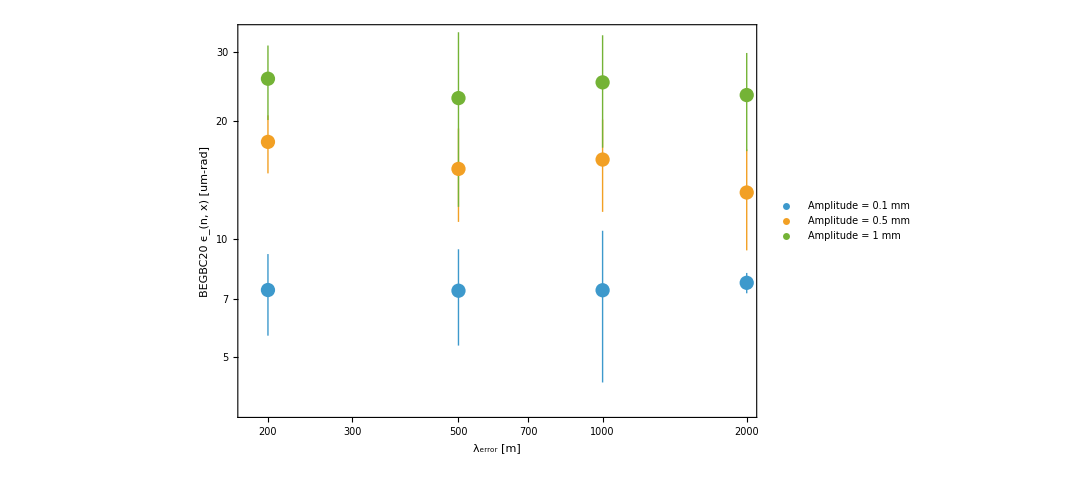

```mathematica
ListLogLogPlot[
Values[GroupBy[data,#[[2]]&]][[All,All,{1,3}]],
ImageSize->800,
LabelStyle->20,
FrameLabel->{"λ_error [m]", "BEGBC20 ϵ_(n, x) [um-rad]"},
Frame->True,
PlotLegends->Placed[{"Amplitude = 0.1 mm","Amplitude = 0.5 mm","Amplitude = 1 mm"},{0.85,0.15}]
]
```